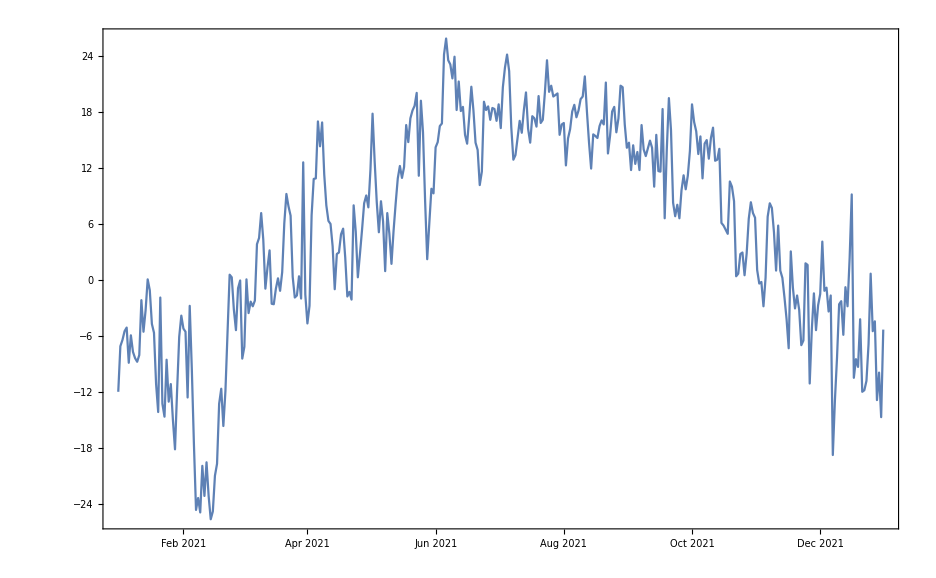

```mathematica
DateListPlot[WeatherData["KMDZ","MeanTemperature",{{2021,1,1},{2021,12,31},"Day"}],Joined->True]
```

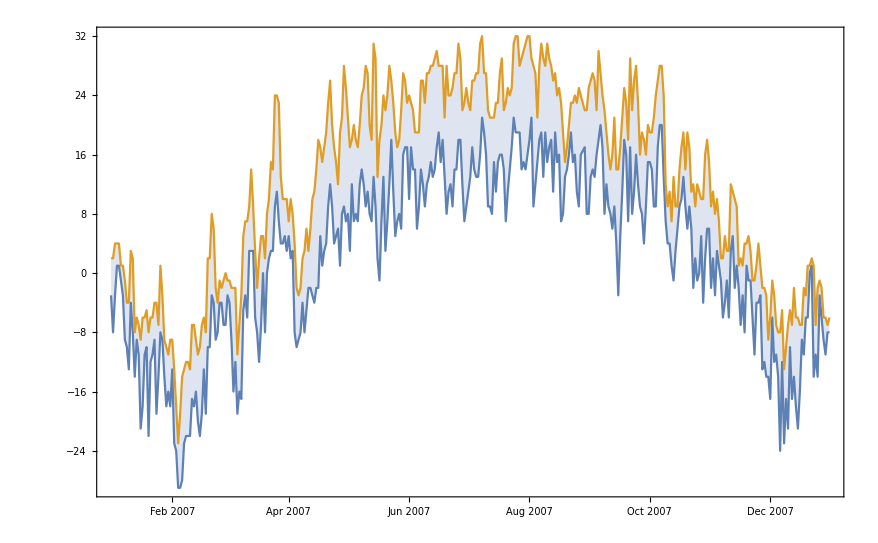

```mathematica
min=WeatherData["KMDZ","MinTemperature",{{2007,1,1},{2007,12,31},"Day"}];
max=WeatherData["KMDZ","MaxTemperature",{{2007,1,1},{2007,12,31},"Day"}];
DateListPlot[{min,max},Joined->True,Filling->{1->{2}}]
```